## VertexOutwardVector-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 18:17:20
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

There are 8 cells in the tissue.

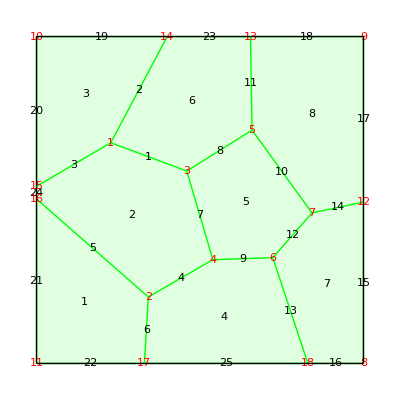

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

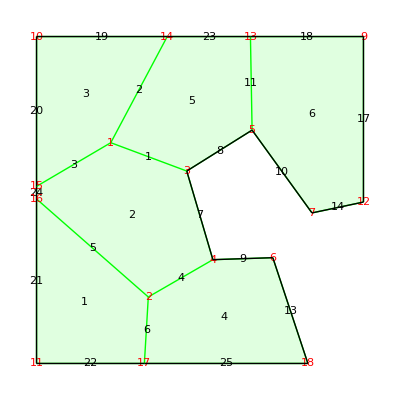

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
map=ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

## Find the outward vectors from each vertex on the boundary

```mathematica
VerticesOnBoundary[S]
```

{3,4,6,18,17,11,16,15,10,14,13,9,12,7,5}

```mathematica
VON=VertexOutwardVector[S,#, True]&/@VerticesOnBoundary[S]
```

{{0.357966,-0.186646},{0.345788,0.249683},{0.636035,0.77166},{0.877005,-0.480481},{-0.0818908,-0.60827},{-0.609253,-0.792976},{-0.702135,0.536787},{-0.713354,-0.298201},{-0.647393,0.762156},{0.2343,0.756528},{0.0267039,0.760463},{0.551466,0.834198},{0.504692,-0.8633},{-0.00131851,-0.999999},{-0.0319512,-0.343082}}

```mathematica
CVC=TissueVertices[S][[VerticesOnBoundary[S]]]
```

{{-4.05117,8.85847},{3.94503,-18.2547},{22.2743,-17.6456},{33.0024,-50.},{-17.0166,-50.},{-50,-50},{-50.,0.319295},{-50.,4.1721},{-50,50},{-10.0171,50.},{15.4304,50.},{50,50},{50.,-0.630427},{34.2523,-3.95181},{15.9343,21.3765}}

#### figure out a good number for the length of the vector

```mathematica
len = .5 * EdgeLengths[S]//Mean
```

15.5007

Observe that the outward vector is nto really normal - it depends on the shape of the nearby tissue boundary.

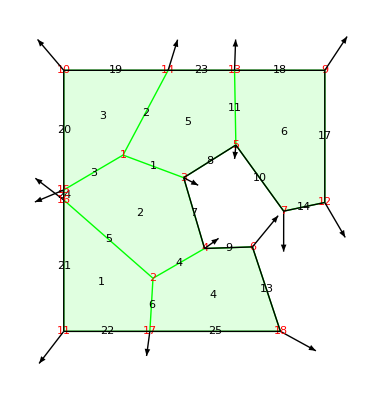

```mathematica
Show[map,Graphics[MapThread[Arrow[{#1,#1+len*#2}]&, {CVC, VON}]]]
```